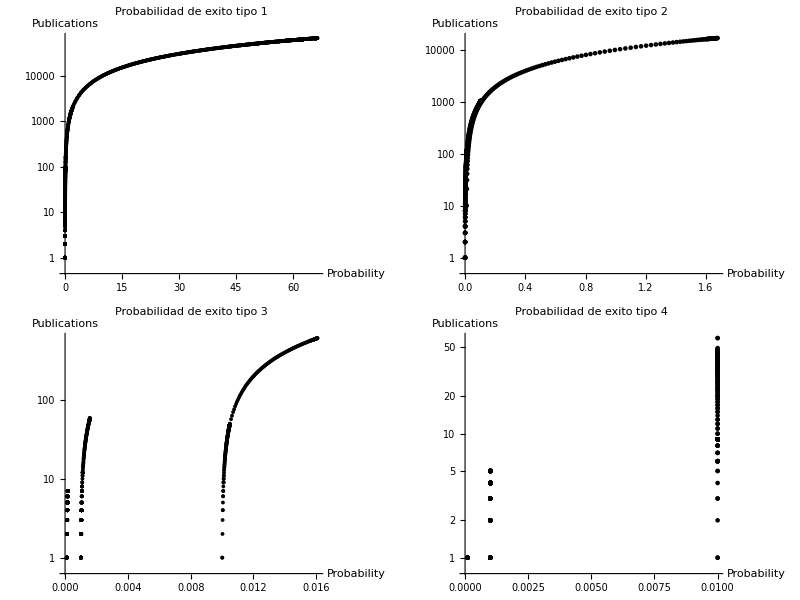

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/ConCompetencia";
SetDirectory[y<>"/images"];
SetOptions[ListLogPlot,BaseStyle->{FontSize->18}];
pub1= Import[y<>"/averageResults/prob-pub-1-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-1-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-1-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-5-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-5-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-5-1.0E-4-100-true-curve.csv"];
plotPub1= Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Probability","Publications"},PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 1",PlotStyle->{{Thick,Black}}]];

Export["prob-pub-1-100-true.png",plotPub1];

pub1= Import[y<>"/averageResults/prob-pub-2-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-2-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-2-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-6-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-6-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-6-1.0E-4-100-true-curve.csv"];
plotPub2 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Probability","Publications"}, PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 2", PlotStyle->{{Thick,Black}}]];
Export["prob-pub-2-100-true.png",plotPub2];

pub1= Import[y<>"/averageResults/prob-pub-3-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-3-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-3-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-7-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-7-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-7-1.0E-4-100-true-curve.csv"];
plotPub3 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Probability","Publications"}, PlotRange->All,PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 3",PlotStyle->{{Thick,Black}}]];
Export["prob-pub-3-100-true.png",plotPub3];

pub1= Import[y<>"/averageResults/prob-pub-4-0.01-100-true-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-4-0.001-100-true-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-4-1.0E-4-100-true-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-8-0.01-100-true-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-8-0.001-100-true-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-8-1.0E-4-100-true-curve.csv"];
plotPub4 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Probability","Publications"},PlotRange->All, PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 4",PlotStyle->{{Thick,Black}}]];
Export["prob-pub-4-100-true.png",plotPub4];

pubTotal=Grid[{{plotPub1,plotPub2},{plotPub3,plotPub4}}]
Export["prob-pub-total-100-true.pdf",pubTotal];
```